## Hexi—PS3—2025-01-24

### Exercises from EIWL3 Section 9

```mathematica
Manipulate[Range[n],{n,0,100}]
```

```mathematica
Manipulate[ListPlot[Range[n]],{n,5,50}]
```

```mathematica
Manipulate[Column[Table[x,n]],{n,1,10}]
```

```mathematica
Manipulate[Graphics[Style[Disk[],Hue[h]]],{h,0,1}]
```

```mathematica
Manipulate[Graphics[Style[Disk[],RGBColor[r,g,b]]],{r,0,1},{g,0,1},{b,0,1}]
```

```mathematica
Manipulate[IntegerDigits[n],{n,1000,9999}]
```

```mathematica
Manipulate[Table[Hue[x],{x,0,1,(1/(n-1))}],{n,5,50}]
```

```mathematica
Manipulate[Table[Graphics[Style[RegularPolygon[6],Hue[x]]],n],{x,0,10},{n,1,10}]
```

```mathematica
Manipulate[Graphics[Style[RegularPolygon[x],color]],{x,5,20},{color,{Red,Yellow,Blue}}]
```

```mathematica
Manipulate[PieChart[Table[n,n]],{n,1,10}]
```

```mathematica
Manipulate[BarChart[IntegerDigits[x]],{x,100,999,1}]
```

```mathematica
Manipulate[RandomColor[n],{n,1,50,1}]
```

```mathematica
Manipulate[Column[x^Range[n]],{x,1,25,1},{n,1,10,1}]
```

```mathematica
Manipulate[NumberLinePlot[Range[10]^n],{n,0,5}]
```

```mathematica
Manipulate[Graphics3D[Style[Sphere[],RGBColor[n,1-n,0]]],{n,0,1}]
```

### Exercises from EIWL3 Section 10

```mathematica
CurrentImage[]
```

-Graphics-

```mathematica
ColorNegate[-Graphics-]
```

-Graphics-

```mathematica
Manipulate[Blur[-Graphics-,x],{x,1,10}]
```

```mathematica
Table[EdgeDetect[Blur[-Graphics-,x]],{x,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageCollage[{-Graphics-,Blur[-Graphics-],EdgeDetect[-Graphics-],Binarize[-Graphics-]}]
```

-Graphics-

```mathematica
ImageAdd[-Graphics-, Binarize[-Graphics-]]
```

-Graphics-

```mathematica
Manipulate[EdgeDetect[Blur[-Graphics-, n]],{n,0,20}]
```

```mathematica
EdgeDetect[Graphics3D[Sphere[]]]
```

-Graphics-

```mathematica
Manipulate[Blur[Graphics[Style[RegularPolygon[5],Purple]],x],{x,0,20}]
```

```mathematica
ImageCollage[Table[Graphics[Style[Disk[],RandomColor[]]],9]]
```

-Graphics-

```mathematica
ImageCollage[Table[Graphics3D[Style[Sphere[],Hue[x]]],{x,0,1,0.2}]]
```

-Graphics-

```mathematica
Table[Blur[Graphics[Disk[]],x],{x,0,30,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageAdd[-Graphics-,Graphics[Disk[]]]
```

-Graphics-

```mathematica
ImageAdd[-Graphics-,Graphics[Style[RegularPolygon[8],Red]]]
```

-Graphics-

```mathematica
ImageAdd[-Graphics-,ColorNegate[EdgeDetect[-Graphics-]]]
```

-Graphics-

### Exercises from EIWL3 Section 11

```mathematica
StringJoin["Hello","Hello"]
```

HelloHello

```mathematica
ToUpperCase[StringJoin[Alphabet[]]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

```mathematica
StringReverse[StringJoin[Alphabet[]]]
```

zyxwvutsrqponmlkjihgfedcba

```mathematica
StringJoin[Table["AGCT",100]]
```

AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT

```mathematica
StringTake[StringJoin[Alphabet[]],6]
```

abcdef

```mathematica
"abcdef"
```

abcdef

```mathematica
StringLength["this is about strings"]
Column[Table[StringTake["this is about strings",x],{x,21}]]
```

21

t
th
thi
this
this 
this i
this is
this is 
this is a
this is ab
this is abo
this is abou
this is about
this is about 
this is about s
this is about st
this is about str
this is about stri
this is about strin
this is about string
this is about strings

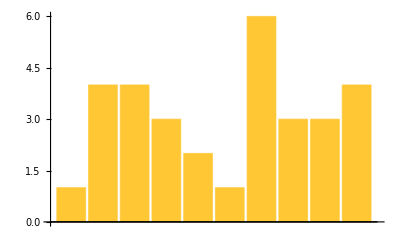

```mathematica
BarChart[StringLength[TextWords["A Long time agp, in a galaxy far, far away"]]]
```

```mathematica
StringLength[WikipediaData["computer"]]
```

60266

```mathematica
Length[TextWords[WikipediaData["computer"]]]
```

9271

```mathematica
Take[TextSentences[WikipediaData["strings"]],1]
```

{String or strings may refer to:}

```mathematica
StringJoin[StringTake[TextSentences[WikipediaData["computer"]],1]]
```

AMTTACCESEMTTTCTPP=ITTDBTTTT==DTLTTTSITIIDMTTAAATTTIASIBIAITITIITSI=CCAHTFTTTAEBNH=ITax()2{,THI=DHTTTTAB==CBTDETTITIRTZTT=PTEITDTTHACIINCTLOTIIIHBT==TTHTVTE=ECWATIHJTIIAATBAIL=TJFCJTHATHTTWITT=TTDTKIHKNNHPNIMTGFTTWISTITS=TTLTTTT=C=A=SH=TC==ATIET=WTTSC=TSC=TCATRDIRTPIWJSAIT=TES=TTSHTALTSG=AETTLSIETWOAMTTRACrRIIISFIIG=IDOHCIAMA=WTOBItSTBSIT=SMSTSS=SSCICW=T=TTMIAL=TITHTFMPWSTCBOTOI=ITTSTTITMWITC=PUTTS=MF=ATHHIT=PALTP=ETHOBSA=CTITTITCITA"=AWA=TMH=TQCVSLTTT=ACARPE=AT=====M

```mathematica
Max[StringLength[TextWords[WordList[]]]]
```

23

```mathematica
Count[StringTake[WordList[],1],"q"]
```

194

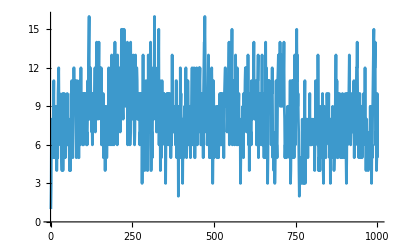

```mathematica
ListLinePlot[StringLength[Take[WordList[],1000]]]
```

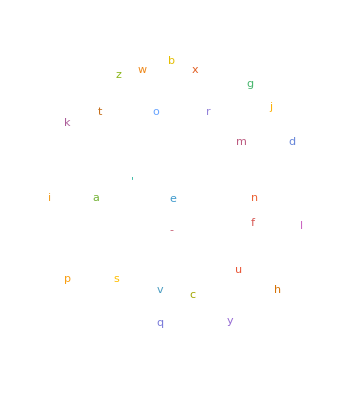

```mathematica
WordCloud[Characters[StringJoin[WordList[]]]]
```